JUST-IN-TIME Tree Transportation Network

Variables

```mathematica
runtime = 50;
p=4;
ein=0;
w=0.1;
```

Number of Entities

```mathematica
NA=1; (* nur 1 A supplier*)
NB1=3;(* number of B suppliers  *)
NC=3; (* number of C suppliers*)
```

#### Natural Frequencies

```mathematica
ωOEM =0.0146; (* OEM *)
ωA =Abs[RandomVariate[NormalDistribution[0.0146,0.0008],NA]]; (* A supplier *)
ωBR=Abs[RandomVariate[NormalDistribution[2.9,0.53],NB1]]; (* B supplier  Cluster 1*)
ωCR=Abs[RandomVariate[NormalDistribution[4.9,4.07],NC]]; (* B supplier Cluster 3*)
```

Coupling upstream

```mathematica
KOEMA=1/NA;
KAB=1/NB1;
KBC=1/NC;
```

Coupling downstream

```mathematica
KAOEM =1/NA;
KBA=1/NB1;
KCB=1/NC;
```

Oscillator Equations

```mathematica
de1=NDSolve[{
(* car manufacturer *)
θ0[1]'[t]==ωOEM- Sum[KOEMA Sin[θ0[1][t]-θ1r[n][t]],{n,NA}],
(* A supplier *)
θ1r[1]'[t]==ωA[[1]]-KAOEM Sin[θ1r[1][t]-θ0[1][t]]- Sum[KAB Sin[θ1r[1][t]-θ2r[m][t]],{m,NB1}],
(* B supplier *)
Table[{θ2r[n]'[t]==ωBR[[n]]
- KBA Sin[θ2r[n][t]-θ1r[1][t]]
- Sum[KBC Sin[θ2r[n][t]-θ3r[m][t]],{m,NC}]},{n,NB1}],

(* C supplier *)
Table[{θ3r[n]'[t]==ωCR[[n]]- Sum[KCB Sin[θ3r[n][t]-θ2r[m][t]],{m,NB1}]},{n,NC}],

Table[θ1r[n][0]==0,{n,NA}],Table[θ2r[n][0]==0,{n,NB1}],Table[θ3r[n][0]==0,{n,NC}],θ0[1][0]==0},
Join[Table[θ1r[n],{n,NA}],Table[θ2r[n],{n,NB1}],Table[θ3r[n],{n,NC}],{θ0[1]}], {t,0,runtime}];
```

___________________________________________________________________________________________________________

```mathematica
Results
```

Results

```mathematica
r1=Sum[Exp[I  θ1r[n][t]],{n,NA}]/NA; l1 =Abs[r1];w1 =Arg[r1]; 
r2=Sum[Exp[I  θ2r[n][t]],{n,NB1}]/NB1;l2 =Abs[r2];wr2 =Arg[r2]; 
r5=(Sum[Exp[I  θ3r[n][t]],{n,NC}])/NC;l5 =Abs[r5];wr5 =Arg[r5];
RAV1=Sum[l1,{t,ein,runtime}]/(runtime-ein);
RAV2=Sum[l2,{t,ein,runtime}]/(runtime-ein);
RAV5=Sum[l5,{t,ein,runtime}]/(runtime-ein);
R1=Evaluate [RAV1/.de1];R2=Evaluate [RAV2/.de1];
R5=Evaluate [RAV5/.de1];
```

```mathematica
data={{R1,R2,R5}};
Text@Grid[Prepend[data,{"A","B1","B2","B3","C"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{{Left,{Center}}},ItemSize->{{8,8,8,8,8,8,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

A | B1 | B2 | B3 | C
{51/50} | {0.651486} | {0.552395} |  |

_____________________________________________________________________________________________________________________________

OEM

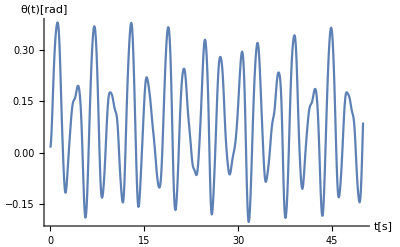

```mathematica
Plot[Evaluate [Table[θ0[1]'[t],{n,NA}]/.de1],{t,ein,runtime},PlotRange->All,LabelStyle->Directive[20],AxesLabel->{"t[s]","θ(t)[rad]"},MaxRecursion->p]
```

A-Supplier

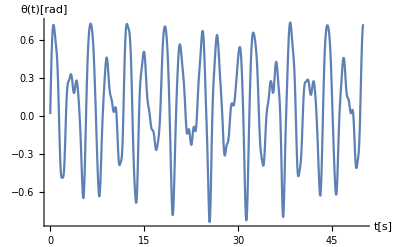

```mathematica
Plot[Evaluate [Table[θ1r[n]'[t],{n,NA}]/.de1],{t,ein,runtime},PlotRange->All,LabelStyle->Directive[20],AxesLabel->{"t[s]","θ(t)[rad]"},MaxRecursion->p]
```

B-supplier

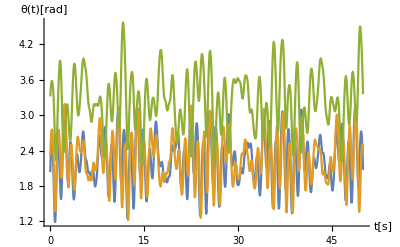

```mathematica
Plot[Evaluate [Table[θ2r[n]'[t],{n,NB1}]/.de1],{t,ein,runtime},PlotRange->All,LabelStyle->Directive[20],AxesLabel->{"t[s]","θ(t)[rad]"},MaxRecursion->p]
```

C-supplier

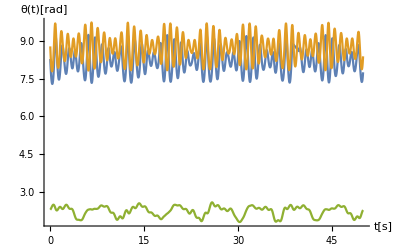

```mathematica
Plot[Evaluate [Table[θ3r[n]'[t],{n,NC}]/.de1],{t,ein,runtime},PlotRange->All,LabelStyle->Directive[20],AxesLabel->{"t[s]","θ(t)[rad]"}]
```

```mathematica
ClearAll;
```